```mathematica
(*setup global parameters*)
ClearAll;
nI =3;
nJ = 3;
nK = 3;
g0Scale= .1;
w0  = 1.67;
g0 = .2;
r0Scale = .01;
numBosons=1000;
highestFreq  = 20*w0;
tf = 4*w0;
(*need to parse files for i j k index*)
(*input file_2_4_463*)
(*output {2,4,463} where elements are integers*)
parserIJK =(ToExpression/@
StringSplit[StringCases[#,RegularExpression["(_\\d{1,3}){3,3}$"]][[1]],"_"])&;
(*Epsilon: probability amplitude cutoff*)
(*Gamma: Spectral intensity of the resevior*)
(*Delta: cavity and emitter frequency spacing*)
paramEpsilon[i_] :=1/highestFreq *  g0Scale*ⅇ^(Log[r0Scale]/nI i);
paramDelta[j_] :=Abs[w0(1-  ⅇ^(Log[2]/nJ j))];
paramGamma[k_] :=numBosons* r0Scale*ⅇ^(Log[g0Scale/r0Scale]/nK k);
printParams[i_,j_,k_]:=StringTemplate["ϵ-> <*paramEpsilon[#i]*>,  ℊ_0-> `g`, ω_0-> <*#w+paramDelta[#j]*>, δ-> <*paramDelta[#j]*>, γ-> <*paramGamma[#k]*>"][<|"i"->i,"j"->j,"k"->k,"g"->g0,"w"->w0|>];
(*file paths *)
base =  "/home/ethan/curr_proj";
pythonOut = base<>"/python_out";
codeOut = base<>"/code_out";
mathematicaOut = base <> "/mathematica_out";
(*important files*)
adaptiveSpin = base<>"/adaptive_spin";
generateSystem = base <> "/generate_energies.py";
configFile = base <> "/parameters.conf";
```

```mathematica
(*generate system files via python*)
pythonArg=
Module[{i,j,k,outputDir=pythonOut,pythonFile=generateSystem,params={},w0=w0},
For[i = 0,i<nI, i++,
For[j = 0, j < nJ, j++,
For[k=0, k< nK, k++,
tmpW0 = w0+paramDelta[j];
tmpW0 = <|"a" -> tmpW0|>;
params= Append[params, {"python" ,pythonFile,StringTemplate[ "--w0=<*paramDelta[#u]+#v*>"][<|"v"->w0,"u"->j|>],
StringTemplate[ "--g0=`a`"][<|"a"->g0|>],
StringTemplate[ "--v0=<*#v*>"][<|"v"->w0|>],
StringTemplate[ "--gamma=<*paramGamma[#p]*>"][<|"p"->k|>],
StringTemplate["--emitter_out=`out`/emitter_out_`i`_`j`_`k`"][<|"out"->outputDir,"i"->i,"j"->j,"k"->k|>],
StringTemplate["--bosons_out=`out`/bosons_out_`i`_`j`_`k`"][<|"out"->outputDir,"i"->i,"j"->j,"k"->k|>],
StringTemplate["-N=`n`"][<|"n"->numBosons|>] } ];
];];];
params
];
RunProcess/@pythonArg;
```

```mathematica
(*pass parameters to adaptive_spin*)
codeArg =Module[{i,j,k,executablePath = adaptiveSpin,codeOut =codeOut,pythonOut=pythonOut, outputFilePath,params={},val,conf=configFile},
For[i = 0, i <nI,i++,
For[j = 0, j < nJ, j++,
For [k = 0, k < nK, k++,
outputFilePath = StringTemplate[codeOut<>"/run_`a`_`b`_`c`"]
[<|"a"->i, "b"->j,"c"->k |>];
params = Append[params,
{executablePath,StringTemplate["--cutoff=<*paramEpsilon[#p]*>"][<|"p"->i|>],
 StringTemplate["--atom_p=`out`/emitter_out_`a`_`b`_`c`"][<|"out"->pythonOut,"a"->i,"b"->j,"c"->k|>],
StringTemplate["--mode_p=`out`/bosons_out_`a`_`b`_`c`"][<|"out"->pythonOut,"a"->i,"b"->j,"c"->k|>], StringTemplate["--output_file=`a`"][<|"a"->outputFilePath|>],StringTemplate["--config=`a`"][<|"a"->conf|>]}];
];];];
params
];
processes= StartProcess/@codeArg;
```

```mathematica
ProcessStatus/@processes
```

{Finished,Finished,Finished,Finished,Finished,Finished,Finished,Finished,Finished,Finished,Finished,Finished,Finished,Finished,Finished,Finished,Finished,Finished,Finished,Finished,Finished,Finished,Finished,Finished,Finished,Finished,Finished}

```mathematica
dataCollection = Module[{mathematicaOut= "/home/ethan/curr_proj/mathematica_out",codeOut="/home/ethan/curr_proj/code_out",pythonOut="/home/ethan/curr_project/python_out",tmpFileList,outputFilePaths},
tmpFileList = mathematicaOut<>"/tmpfiles";
Run["ls "<> codeOut<>  " > " <> tmpFileList];
tmpFileList = Import[tmpFileList,"String"];
Pause[.01];
outputFilePaths=StringCases[tmpFileList,RegularExpression["run(_\\d{1,3}){3,3}"]];
({Import[codeOut<>"/"<>#,"Table"],parserIJK[#]})&/@outputFilePaths
];
Length[dataCollection]
```

27

```mathematica
pltList=
Module[{i,data,q,params,pUp,pDown,pltTmp,plts={},sortedPlts=Table[{},{i,1,nI},{j,1,nJ},{k,1,nK}]},
For[i = 1, i ≤Length[dataCollection],i++,

data = dataCollection[[i]][[1]];
q =  dataCollection[[i]][[2]];
params =printParams[q[[1]],q[[2]],q[[3]]];
pUp = Table[{data[[j]][[1]],data[[j]][[2]]},{j,1,Length[data]-2}];
pDown = Table[{data[[j]][[1]],data[[j]][[3]]},{j,1,Length[data]-2}];
pltTmp = {{ListPlot[{pUp,pDown},PlotLabel->"Probability of Emitter vs Time (ℏ = eV = 1) \n " <> params,AxesLabel->{"time (ℏ/eV ~ 6*10^-16)"},PlotLegends->{"e","g"},ImageSize->Medium],
ListLogPlot[{pUp,pDown},PlotLabel->"Probability of Emitter vs Time (ℏ = eV = 1)\n" <> params,AxesLabel->{"time (ℏ/eV ~ 6*10^-16)"},PlotLegends->{"e","g"},ImageSize->Medium]},q};
sortedPlts[[q[[1]]+1]][[q[[2]]+1]][[q[[3]]+1]]=pltTmp;
];
sortedPlts
];
Manipulate[pltList[[i]][[j]][[k]][[1]][[2]],{i,1,nI,1},{j,1,nJ,1},{k,1,nK,1}]
```

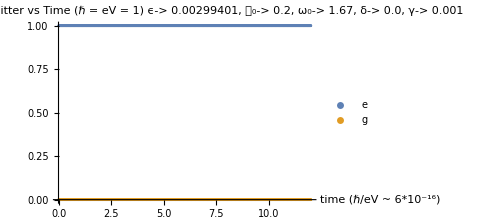

```mathematica
pltList[[1]][[1]][[1]][[1]][[1]]
```